```mathematica
(* Travelling Salesman Simulated Annealing *)


(* define functions *)

(*generate a new path given an existing one *)
(* the generation type can be either swap or move *)
Swap[path_]:=
Module[{newPath,indexA,indexB,valueA, valueB},
indexA = RandomInteger[{1,Length[path]}];
indexB = RandomInteger[{1,Length[path]}];
valueA = path[[indexA]];
valueB = path[[indexB]];
(* swap *)
newPath = ReplacePart[path, indexB->valueA];
newPath = ReplacePart[newPath, indexA->valueB];
newPath
];

Move[path_]:=
Module[{newPath,indexA, indexB,valueA,valueB},
indexA = RandomInteger[{1,Length[path]}];
indexB = RandomInteger[{1,Length[path]+1}];
valueA = path[[indexA]];
newPath = Insert[path,valueA, indexB];
If[indexA > indexB, Delete[newPath,indexA+1],Delete[newPath,indexA]]
];

(* For a given path, calculate the distance *)
CalculateDistance[salesmanPath_] := 
Module[{totalLen},
totalLen = 0;
Do[
totalLen +=EuclideanDistance[salesmanPath[[i]],salesmanPath[[i+1]]];
,{i,1,Length[salesmanPath]-1}
];
(*account for closing the loop*)
totalLen += EuclideanDistance[salesmanPath[[1]],salesmanPath[[-1]]];
totalLen
];

(* Determine if we accept the new path *)
(* takes in two route lengths and a temperature *)
AcceptNewRoute[currentRouteLength_,proposedRouteLength_,temperature_]:=
Module[{thresholdAccept},
thresholdAccept = E^(-(proposedRouteLength-currentRouteLength)/temperature);
RandomReal[] < thresholdAccept
];

(* Calculate Temperature *)
(* note constants for init temperature and decay rate *)
CalculateTemperature[iteration_, nIterations_]:=
Module[{initTemperature, decayRate},
initTemperature = 1;
decayRate = 5.0;
initTemperature*(1-(decayRate/nIterations))^iteration
];
(* Iteration Types *)
SimulatedAnnealingMoveIteration[currentRoute_,temperature_]:=
Module[{newRoute},
newRoute = Move[currentRoute];
If[AcceptNewRoute[CalculateDistance[currentRoute ],CalculateDistance[newRoute],temperature],
newRoute,
currentRoute
]
];
SimulatedAnnealingSwapIteration[currentRoute_,temperature_]:=
Module[{newRoute},
newRoute = Swap[currentRoute];
If[AcceptNewRoute[CalculateDistance[currentRoute ],CalculateDistance[newRoute],temperature],
newRoute,
currentRoute
]
];
```

```mathematica
(*define cities*)
nCities = 10;
(* generate some initial path *)
currentRoute = RandomReal[{0.1},{nCities,2}];
currentRouteSwap = currentRoute;
(* define number of iterations *)
nIterations = 100000;
moveTable = Table[
temperature = CalculateTemperature[iteration,nIterations];
currentRoute = SimulatedAnnealingMoveIteration[currentRoute,temperature];
CalculateDistance[currentRoute]
, {iteration,1,nIterations}
];
swapTable = Table[
temperature = CalculateTemperature[iteration,nIterations];
currentRouteSwap = SimulatedAnnealingSwapIteration[currentRouteSwap,temperature];
CalculateDistance[currentRouteSwap]
, {iteration,1,nIterations}
];
```

0.449912

0.450263

0.0838692

0.084565

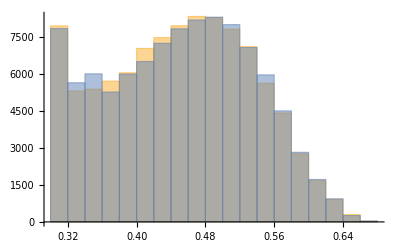

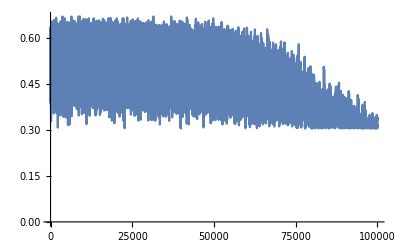

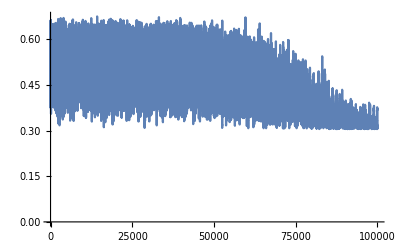

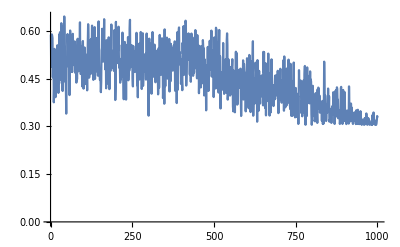

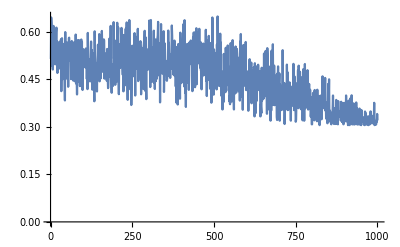

```mathematica
Mean[moveTable]
Mean[swapTable]
StandardDeviation[moveTable]
StandardDeviation[swapTable]
Histogram[{moveTable,swapTable}]
ListLinePlot[moveTable]
ListLinePlot[swapTable]

filteredMoveTable = moveTable[[;;;;100]];
ListLinePlot[filteredMoveTable]
filteredSwapTable = swapTable[[;;;;100]];
ListLinePlot[filteredSwapTable]
```